```mathematica
matelem[k_,kp_]=Exp[-I*(2*k-Np)*ϕ/2]*Sqrt[((k!)*((Np-k)!)*(kp!)*((Np-kp)!))]*Sum[(((-1)^n)*(Cos[θ/2]^(k-kp+Np-2*n))*(Sin[θ/2]^(2*n+kp-k)))/(((k-n)!)*((Np-kp-n)!)*(n!)*((n+kp-k)!)),{n,Max[k-kp,0],Min[k,Np-kp]}];
```

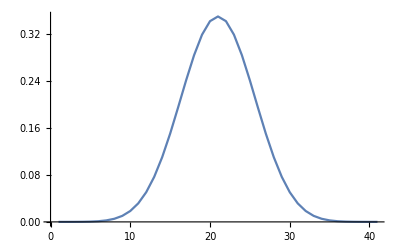

{5.28942×10^-6,0.0000171558,0.0000573422,0.000172162,0.000464242,0.00113666,0.00255263,0.00530136,0.0102488,0.0185404,0.0315188,0.0505261,0.0765921,0.110046,0.150145,0.19483,0.240739,0.283533,0.318522,0.341488,0.349494,0.341488,0.318522,0.283533,0.240739,0.19483,0.150145,0.110046,0.0765921,0.0505261,0.0315188,0.0185404,0.0102488,0.00530136,0.00255263,0.00113666,0.000464242,0.000172162,0.0000573422,0.0000171558,5.28942×10^-6}

```mathematica
Np=40;θ=Pi/2.0;ϕ=0;
mat=Table[matelem[k,kp],{k,0,Np},{kp,0,Np}];
Amat={};
For[k=0,k≤Np,k=k+1,
Amatline={};
For[kp=0,kp≤Np,kp=kp+1,
aelem=Sum[mat[[k+1,k1+1]]*mat[[kp+1,k1+1]]*mat[[k+1,k2+1]]*mat[[kp+1,k2+1]]*mat[[k+1,Np-k1-k2+1]]*mat[[kp+1,Np-k1-k2+1]],{k1,0,Np},{k2,0,Np-k1}];
Amatline=Append[Amatline,aelem];
];
Amat=Append[Amat,Amatline];
];
psielem=Eigenvectors[Amat,1][[1]];
psielem=Sign[psielem[[1]]]*psielem;
p2=ListPlot[psielem,Joined->True];
Print[p2];
Print[psielem];
```

{9.53674×10^-7,6.03157×10^-6,0.0000266347,0.0000947935,0.000288303,0.000773599,0.00186842,0.00411779,0.00836328,0.0157699,0.0277659,0.0458538,0.0712826,0.104614,0.145281,0.191271,0.239089,0.28408,0.321121,0.345544,0.354077,0.345544,0.321121,0.28408,0.239089,0.191271,0.145281,0.104614,0.0712826,0.0458538,0.0277659,0.0157699,0.00836328,0.00411779,0.00186842,0.000773599,0.000288303,0.0000947935,0.0000266347,6.03157×10^-6,9.53674×10^-7}

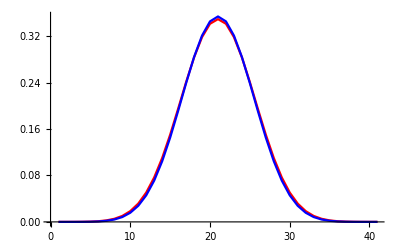

```mathematica
psicomp=Normalize[Table[N[Binomial[Np,k]^(1/2)],{k,0,Np}]]
ListPlot[{psielem,psicomp},Joined->True,PlotStyle->{Red,Blue}]
```

```mathematica
psicomp.psielem
```

0.99982